```mathematica
bookwinnersDataset=Import["C:\\Users\\hekim\\Box Sync\\wheaton\\Papers\\Works in Progress\\Testing 4.10 II.xlsx",{"Dataset",1},HeaderLines->1]
```

Dataset[<>]

Convert the Dataset to its simplified form, a list of associations:

```mathematica
bookWinners=Normal[bookwinnersDataset]
```

{<|Year→2017.,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,5,Publisher→University of Minnesota|>,2537,<|1|>}
 |  |  |  |

```mathematica
Dimensions@bookwinnersDataset
```

{2539,8}

```mathematica
First@bookwinnersDataset
```

Dataset[<>]

Delete the empty strings at level 2 (values of each association in the list) in bookwinners:

```mathematica
Dataset[bookWinnersClean=DeleteCases[bookWinners,"",{2}]]
```

Dataset[<>]

Gather the rows by book titles to form “subtables”:

```mathematica
gatheredBookWinners=GatherBy[bookWinnersClean,#["Book Title"]&]
```

{{1},61,{1}}
 |  |  |  |

Display the gathered rows as a Dataset:

```mathematica
gatheredBookWinners//Dataset
```

Dataset[<>]

Get the first subtable from gatheredBookWinners: (like using “sortyby in Excel”)

```mathematica
gatheredBookWinners[[1]]//Dataset
```

Dataset[<>]

Merge each of the subtables into a single row, collecting all distinct values of each key into a list:

```mathematica
Dataset[mergedBookWinners=Merge[#,Union]&/@gatheredBookWinners]
```

Dataset[<>]

Get the first element of each list of distinct values for all keys except “Academic Acknowledgements”:

```mathematica
Dataset[condensedBookWinners=MapIndexed[(If[
First[#2]===Key["Academic Acknowledgements"],
#1,
First[#1]
]&),#]&/@mergedBookWinners]
```

Dataset[<>]

Map Floor onto the value of each Year key to convert it to an integer:

```mathematica
Dataset[integerYearBookWinners=MapAt[Floor,condensedBookWinners,{All,Key["Year"]}]]
```

Dataset[<>]

```mathematica
authors = integerYearBookWinners[[2;;,3]]
```

{Roberto G. Gonzales,Carla Shedd,Laurence Ralph,Nancy DiTomaso,54,Travis Hirschi and Hanan C. Selvin,Jerome H. Skolnick,Robert Boguslaw,David Matza}
 |  |  |  |

Accounting for co-authors

```mathematica
Select[authors,StringContainsQ[#," and "]&]
```

{John Hagan and Bill McCarthy,Melvin L. Oliver and Thomas M. Shapiro,Joyce Rothschild and J. Allen Whitt,Frances Fox Piven and Richard A. Cloward,Travis Hirschi and Hanan C. Selvin}

```mathematica
StringSplit["John Hagan and Bill McCarthy"," and "]
```

{John Hagan,Bill McCarthy}

```mathematica
First@authors
```

Roberto G. Gonzales

```mathematica
StringSplit["Roberto G. Gonzales", " and "]
```

{Roberto G. Gonzales}

```mathematica
splitAuthors[authorString_String]:=StringSplit[authorString, " and "]
```

```mathematica
integerYearBookWinners//Take[#,3]&
```

{<|Year→2017,6,Publisher→University of Minnesota|>,<|Year→2016,6,Publisher→32|>,<|Year→2015,6,Publisher→Russell Sage Foundation|>}
 |  |  |  |

```mathematica
Dataset[integerYearBookWinnersSplitAuthors=MapAt[splitAuthors,integerYearBookWinners,{All,"Author"}]]
```

Dataset[<>]

finding where this notebook is

```mathematica
NotebookDirectory[]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\

```mathematica
FileNameJoin[{NotebookDirectory[],"Up to Co-Authors.m"}]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\Up to Co-Authors.m

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Up to Co-Authors.m"}],integerYearBookWinnersSplitAuthors]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\Up to Co-Authors.m

```mathematica
integerYearBookWinnersSplitAuthors =Import[ "C:\\Users\\hekim\\Documents\\WSS-Template\\Final Project\\Drafts FINAL PROJECT\\Up to Co-Authors.m"]
```

{<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,5,Publisher→University of Minnesota|>,61,<|1|>}
 |  |  |  |

### IS THIS THE VARIABLE THAT HAS THE CLEAN DATA?

```mathematica
integerYearBookWinnersSplitAuthors
```

{<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,5,Publisher→University of Minnesota|>,61,<|1|>}
 |  |  |  |

### These are alternative ways to select a single year or a range

```mathematica
bookWinnersForYear[year_]:=Select[integerYearBookWinnersSplitAuthors,#Year===year&]
```

```mathematica
bookWinnersBetweenYears[from_,to_]:=Select[integerYearBookWinnersSplitAuthors,Between[#Year,{from,to}]&]
```

```mathematica
bookWinnersForYear[1994]
```

{<|Year→1994,Book Title→What Machines Can't Do: Politics and Technology in the Industrial Enterprise,Author→{Robert Thomas},Academic Acknowledgements→{Bob Cole,Ed Schein,Jan Odhnoff,John Van Maanen,Kent Bowen,Lotte Bailyn,Michael Unseem,Mike Piore,Paul Lagace,Paul Osterman,Rebecca Henderson,Rosanna Hertz,Tom Kochan,Tom Magnanti},Authors' Institution @ Publication→Massachusetts Institute of Technology,Author UG→UC, Santa Cruz,Author PhD→Northwestern University,Publisher→University of California Press|>}

```mathematica
bookWinnersBetweenYears[1994,1998]
```

{<|Year→1998,Book Title→The Making of the Unborn Patient: A Social Anatomy of Fetal Surgery,5,Publisher→Rutgers University Press|>,4,<|1|>}
 |  |  |  |

Per each book, create the edges, starting with one and then for all, and combine all of them
Use Values@ to drop the keys and just get the lists

```mathematica
Values@integerYearBookWinnersSplitAuthors[[1,{3,4}]]
```

{{Claudia G.Cervantes-Soon},{Angela Valenzuela,Aurolyn Luykx,Carol Brochin,Cecilia Balli,Douglas E. Foley,Elaine Hampton,Elizabeth Villareal,G. Sue Kasun ,Haydee Rodriguez,Keffrelyn Brown,Lourdes Diaz Soto,Luis Urrieta,Monica Neshyba,Toni Avila}}

```mathematica
Outer[DirectedEdge,{a,b,c},{4,5}]
```

{{a->4,a->5},{b->4,b->5},{c->4,c->5}}

### All Years

```mathematica
edges=Join@@(Join@@Outer[DirectedEdge,Sequence@@Values@#]&)/@integerYearBookWinnersSplitAuthors[[All,{3,4}]];
Length[edges]
```

2667

### Between Years - Enter the year ranges

```mathematica
edges=Join@@(Join@@Outer[DirectedEdge,Sequence@@Values@#]&)/@bookWinnersBetweenYears[1994,1998][[All,{3,4}]];
Length[edges]
```

406

### SIngle Year

```mathematica
edges=Join@@(Join@@Outer[DirectedEdge,Sequence@@Values@#]&)/@bookWinnersForYear[1994][[All,{3,4}]];
Length[edges]
```

14

BOB - what is this line doing? Is it needed?

```mathematica
Map[Outer[DirectedEdge,]&,integerYearBookWinnersSplitAuthors[[All,{3,4}]]
```

### Data cleaning

testing if there is a missing person from acknowledgements - does not need to be evaluated
The names in the “author” column, and only this column, are surrounded by {}

```mathematica
integerYearBookWinners[[All,"Author"]]//Sort//Column
```

1
 |  |  |  |

```mathematica
Select[integerYearBookWinners[[All,{"Year","Academic Acknowledgements"}]],Length[#["Academic Acknowledgements"]]==0&]
```

{}

```mathematica
integerYearBookWinners[[All,"Year"]]
```

{2017,2016,2015,2014,2013,2012,2011,2010,2009,2008,2007,2006,2005,2004,2003,2002,31,1977,1976,1975,1974,1973,1973,1972,1971,1970,1969,1968,1967,1967,1966,1965,1964}
 |  |  |  |

### Preparing the Data

(A large amount of time was spent with Jesse 6/30/19 to get the more usable - time with Jesse cleaning data mills)
											
											Tasks done Y/N
A. Remove typos [what if someone won it more than once?] Not possible?
Do: integerYearBookWinners[[All,”Author”]]//Sort//Column

B. Adjust for missing values N
C. Adjust for co-winners N
D. Adjust for different spellings of the same person N
E. Adjust for one known missing year (book) N
F. Adjust for co-authors (multiple edges?) N look for “ and “

E. Change Columns accordingly for future analysis N

Column Five

```mathematica
authorsInstitution =Rest@bookwinnersDataset;
authorsInstitution[[All,5]];
Iconize[%]
```

Column Three

```mathematica
allAuthors =Rest@bookwinnersDataset;
authorsInstitution[[All,3]];
Iconize[%]
```

### Connecting Authors and Acknowledged

The graph does work with the new variable with Bob (07/01/19) and he helped me on this day to account for dual authorship

```mathematica
edges[[1]]//InputForm
```

DirectedEdge["Robert Thomas", "Bob Cole"]

### This is a complete graph including disconnected networks

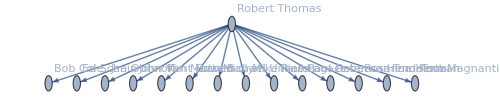

```mathematica
graph=Graph[edges, VertexLabels -> "Name",ImageSize -> 500]
```

### This is a graph with the disconnected networks removed

```mathematica
g2=ConnectedComponents[Graph[ReplaceAll[edges,DirectedEdge->UndirectedEdge], VertexLabels -> "Name",ImageSize -> 500]];
maincomponentvertices=MaximalBy[g2,Length];
coreGraph=Subgraph[graph,maincomponentvertices]
```

-Graphics-

### Social Network Analysis (SNA)

Need to make graph (g) and coreGraph (cg) 
Year, Range of Years, All Years and respective SNA metrics

The total number of years

```mathematica
Length@integerYearBookWinnersSplitAuthors[[All,1]]
```

63

The span of years to create a time series

```mathematica
integerYearBookWinnersSplitAuthors[[All,1]]//MinMax
```

{1964,2017}

### Time Series

```mathematica
v={2,1,6,5,7,4};
t={1,2,5,10,12,15};
ts=TimeSeries[v,{t}]
```

TimeSeries[…]

t = years
v = SNA metrics (in-degrees, SNA metrics, etc.)

TimeSeries[…]

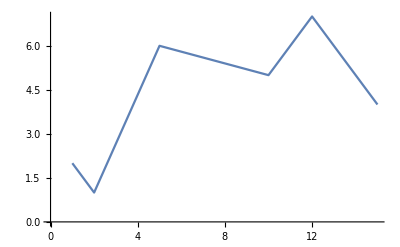

```mathematica
ListLinePlot[ts]
```

E. Which nodes or patterns (associations) emerge?

### Test (A Heuristic List)

A) Dunbar’s Rule	N = 150
B) Zipf’s		Kth is 1/k of the 1st number	(zipf distribution)
C) Sarnoff’s		V = n
D) Odlyzko’s		n log(n)
E) Metcalfe’s		V = n^2
F) Reed’s		V = 2^n
G) Feigenbaum	(x3-x2)/(x2-x1) = F Constant
Other rules/laws whereby I really start rambling into Neverland 
H) Cellular Automata?
I) Agent Based Modeling? 
J) Self-Organized Criticality?
K) Phase Transitions? 
L) Fractal Geometry
N) Built-in Mathematica tests?
O) Machine Learning tests?

### Visualizations

A. Highlight Key vertices or edges 
B. A Manipulate Function of time
Shortest Path?
CommunityGraphPlot (to show isolates?)

HOW come I cannot make a simple BARCHART?